# fit_spotsize.nb

## Least squares fit to determine the gaussian beam width (spotsize)

Version of 12 Apr 2010 (Sasa)

## 1. Data

```mathematica
powers={56.7,56.6,56.6,56.5,56.4,56.3,56.1,55.7,55.0,54.1,52.7,51.2,49.1,46.3,42.9,39.0,34.8,30.7,26.2,21.8,17.8,14.8,11.5,8.2,6.2,4.4,3.1,2.2,1.6,1.1,0.8,0.6,0.5,0.4,0.3,0.3, 0.3,0.3};
```

```mathematica
knifehights=50Range@Length@powers//N;
```

```mathematica
data=Transpose@{knifehights,powers};
```

```mathematica
n=Length[data]
```

38

## 2. Model

```mathematica
params={p0,p1,h0,w}
```

{p0,p1,h0,w}

```mathematica
modelfn[x_,{p0_,p1_,h0_,w_}]:=p0+p1/2(1-Erf[√2(x-h0)/w])
```

```mathematica
s2fn[data_,params_]:=Module[{m,d,x=First/@data,y=Last/@data},
m=modelfn[#,params]&/@x;
d=y-m;
d.d
]
```

```mathematica
m=Length[params]
```

4

## 3. Fit

```mathematica
pfit=FindFit[data,{modelfn[x,params],
0<p0<10,0<p1<100,500<h0<1500,100<w<1000
},params,x]
```

{p0→0.367603,p1→56.3763,h0→925.306,w→511.596}

```mathematica
D[s2fn[data,params],#]&/@params/.pfit//N
```

{-0.000228,-0.00516183,-0.000392784,-0.0000271739}

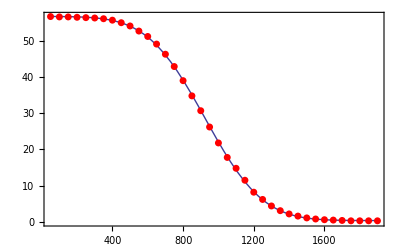

```mathematica
Plot[modelfn[x,params/.pfit],{x,Min[First/@data],Max[First/@data]},PlotStyle->Thick,Frame->True,Epilog->{Red,AbsolutePointSize[5],Point/@Transpose@{First/@data,Last/@data}}]
```

## 4. Parameter errors

```mathematica
s2min=s2fn[data,params/.pfit]
```

0.99945

```mathematica
rms=√(s2min/(n-m))
```

0.171451

```mathematica
atamat=1/2 Outer[D[(n-m)/s2min s2fn[data,params],#1,#2]&,params,params]/.pfit//N
```

{{1292.71,612.552,38.3471,0.0117354},{612.552,514.372,19.1703,-5.39482},{38.3471,19.1703,2.38473,-0.00492761},{0.0117354,-5.39482,-0.00492761,0.298395}}

```mathematica
covmat=Inverse[atamat]
```

{{0.00310791,-0.0035993,-0.0211777,-0.0655454},{-0.0035993,0.00795404,-0.00576548,0.143851},{-0.0211777,-0.00576548,0.806039,-0.0900931},{-0.0655454,0.143851,-0.0900931,5.9531}}

```mathematica
pstderr=Table[covmat[[i,i]],{i,m}]//Sqrt
```

{0.0557487,0.0891854,0.897797,2.4399}

## 5. Summary

```mathematica
MapThread[Print[StringJoin[#1," = ",#2," +/- ",#3]]&,Map[ToString,{params,params/.pfit,pstderr},{2}]];
```

p0 = 0.367603 +/- 0.0557487

p1 = 56.3763 +/- 0.0891854

h0 = 925.306 +/- 0.897797

w = 511.596 +/- 2.4399